```mathematica
Subscript[p, r]=(α(a+c+aα+2cα)+a(2+3α)θ+α(1+2α)Subscript[c, m])/(2(1+α)(1+2α))+(−c+aθ+α Subscript[c, m]+(−1−α+μ α)Subscript[c, r])/(2(1+α)(−2+Subscript[τ, r]))
```

```mathematica
pr1=(-c+a θ+α Subscript[c, m]+Subscript[c, r] (-1-α+μ α))/(2 (1+α) (-2+Subscript[τ, r]))+(θ a(2+3 α)+Subscript[c, m] α(1+2 α)+α(a+c+a α+2 c α))/(2 (1+α) (1+2 α))
```

(α (a+c+a α+2 c α)+a (2+3 α) θ+α (1+2 α) c_m)/(2 (1+α) (1+2 α))+(-c+a θ+α c_m+c_r (-1-α+μ α))/(2 (1+α) (-2+τ_r))

```mathematica
pr0=((a+2c)α)/(2(1+2α))+(α Subscript[c, m]+(1+α−αμ)Subscript[c, r])/(4(1+α))+((3+4α)aθ)/(4(1+α)(1+2α))
```

((a+2 c) α)/(2 (1+2 α))+(a (3+4 α) θ)/(4 (1+α) (1+2 α))+(α c_m+(1+α-α μ) c_r)/(4 (1+α))

```mathematica
pr1-pr0=-((a+2 c) α)/(2 (1+2 α))-(a (3+4 α) θ)/(4 (1+α) (1+2 α))+(α (a+c+a α+2 c α)+a (2+3 α) θ+α (1+2 α) Subscript[c, m])/(2 (1+α) (1+2 α))-(α Subscript[c, m]+(1+α-α μ) Subscript[c, r])/(4 (1+α))+(-c+a θ+α Subscript[c, m]+Subscript[c, r] (-1-α+μ α))/(2 (1+α) (-2+Subscript[τ, r]))
```

-((a+2 c) α)/(2 (1+2 α))-(a (3+4 α) θ)/(4 (1+α) (1+2 α))+(α (a+c+a α+2 c α)+a (2+3 α) θ+α (1+2 α) c_m)/(2 (1+α) (1+2 α))-(α c_m+(1+α-α μ) c_r)/(4 (1+α))+(-c+a θ+α c_m+c_r (-1-α+μ α))/(2 (1+α) (-2+τ_r))

```mathematica
prcha=-((a+2 c) α)/(2 (1+2 α))-(a (3+4 α) θ)/(4 (1+α) (1+2 α))+(α (a+c+a α+2 c α)+a (2+3 α) θ+α (1+2 α) Subscript[c, m])/(2 (1+α) (1+2 α))-(α Subscript[c, m]+(1+α-α μ) Subscript[c, r])/(4 (1+α))+(-c+a θ+α Subscript[c, m]+Subscript[c, r] (-1-α+μ α))/(2 (1+α) (-2+Subscript[τ, r]))
```

-((a+2 c) α)/(2 (1+2 α))-(a (3+4 α) θ)/(4 (1+α) (1+2 α))+(α (a+c+a α+2 c α)+a (2+3 α) θ+α (1+2 α) c_m)/(2 (1+α) (1+2 α))-(α c_m+(1+α-α μ) c_r)/(4 (1+α))+(-c+a θ+α c_m+c_r (-1-α+μ α))/(2 (1+α) (-2+τ_r))

```mathematica
prcha=FullSimplify[prcha]
```

(-2 c+(-2 c α+a θ+2 a α θ+α (1+2 α) c_m) τ_r+(1+2 α) c_r (-2 α μ+(-1+α (-1+μ)) τ_r+2 μ α))/(4 (1+α) (1+2 α) (-2+τ_r))

```mathematica
prchafenzi=(-2 c+(-2 c α+a θ+2 a α θ+α (1+2 α) Subscript[c, m]) Subscript[τ, r]+(1+2 α) Subscript[c, r] (-2 α μ+(-1+α (-1+μ)) Subscript[τ, r]+2 μ α))
```

-2 c+(-2 c α+a θ+2 a α θ+α (1+2 α) c_m) τ_r+(1+2 α) c_r (-2 α μ+(-1+α (-1+μ)) τ_r+2 μ α)

```mathematica
α=0.4
```

0.4

```mathematica
prchafenzi=Simplify[prchafenzi]
```

-4.72+18.2 τ_r+3.6 μ α

```mathematica
-4.719999999999999+18.199999999999996 Subscript[τ, r]+3.6 μ α
```

```mathematica
prcha=-3.9999999999999987+18.199999999999996 Subscript[τ, r]
```

-4.+18.2 τ_r

```mathematica
-2 c+(-2 c α+a (1+2 α) θ+α (1+2 α) Subscript[c, m]) Subscript[τ, r]+(1+2 α) Subscript[c, r] (-2 α μ+(-1+α (-1+μ)) Subscript[τ, r]+2 μ α)
```

-4+(20.+0.72 2_m) τ_r+1.8 (-0.4-1.2 τ_r+2 μ α)

```mathematica
Reduce[prchafenzi<0&&c>0&&α>0&&θ>0&&0<Subscript[τ, r]<1&&Subscript[c, m]>0&&Subscript[c, r] >0&&0<μ<1]
```

Reduce[-2 c+(-2 c α+a (1+2 α) θ+α (1+2 α) c_m) τ_r+(1+2 α) c_r (-2 α μ+(-1+α (-1+μ)) τ_r+2 μ α)<0&&c>0&&α>0&&θ>0&&0<τ_r<1&&c_m>0&&c_r>0&&0<μ<1]

```mathematica
α=0.5
```

```mathematica
a=20
c=2  
Subscript[c, r]=1
Subscript[c, m]=0.5
θ=0.6  
α=0.4
```

20

2

1

0.5

0.6

0.4

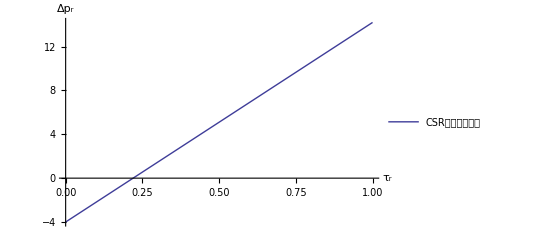

```mathematica
pic1=Plot[{prcha},{Subscript[τ, r],0,1},AxesLabel->{Subscript[τ, r],Subscript[Δp, r]},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"CSR与零售价关系"},LegendLayout->{"Row",1}],{0.75,0.1}]]
```